# Sample post

Few weeks ago I ventured in the possibility of creating a median generating function. There, it is shown that the median satifies:

𝕄d[X] = argmin_v 𝔼[|X-v|]

I didn’t mentioned there, but it is also true that

𝔼[X] = argmin_v 𝔼[(X-v)^2]

which looks like a circular definition but it suggested to Huber (in 1964) that all those location estimators could be described by general pattern. Huber noticed that they included a notion of distance between the estimate and the samples. This is, if you have {X_i}_(i=1..n) realisations of a random variable, then certainly one can write the median and mean using the following estimators:

OverHat[x_M] =  argmin_v 1/n∑_(i=1)^n |X_i-v|, and

x̂ =  argmin_v 1/n∑_(i=1)^n (X_i-v)^2

The similarities are stricking! So, enter Huber’s M-estimators... what if instead of |X_i-t|, or (X_i-t)^2 you allow to use other notions of distance? Huber just did that and opened the door to what today are called M-estimators. Actually, the one I am going to describe below, he defined it in terms of the derivative. Why? Because the derivative is the tool you would use in calculus (see previous post about the median) to find the minimum. In this setting

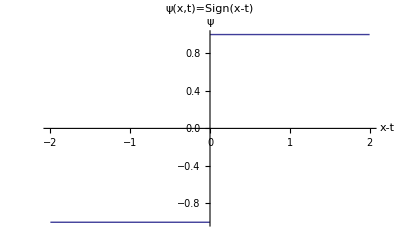

```mathematica
Plot[Sign[u],{u,-2,2},AxesLabel->{"x-t","ψ"},PlotLabel->Style["ψ(x,t)=Sign(x-t)",{Bold,Italic}]]
```

and this interactive plot lets you play with k in Huber’s ψ to see how it is actually something in the middle.

```mathematica
Manipulate[Plot[Piecewise[{{k,u≥k},{u,u≥-k && u <k},{-k,u<-k}}],{u,-2,2},AxesLabel->{"x-t","ψ"}],{k,0,2}]
```

Recaping: mean and median may be seen as an special case of the more general

argmin_t∫ϕ(X,t)dX

which can be recasted - if we can use calculus - as

solve for t,∫ψ(X,t)dX = 0, where ψ(x,t) = ⅆ/ⅆt ϕ(x,t)

which, in turn, becomes for a particular sample {X_i} the statistic T_n

T_n = solve for t,1/n∑_(i=1)^n ψ(X_i,t) = 0

although you would iterate that (somehow) to have a better approximation.

One would impose certain conditions on ψ (or ϕ), so the statistic T_n behaves properly; but I would leave it to the reader to think about what conditions would be appropriate for ψ (or ϕ).